Hi Bella:
I turned the a parameter up until it became one around.  Grabbed a point on the once around loop and stuck the point on the graph of the loop.

```mathematica
Clear[TMax,f,t,y,ySol, yEnd]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:={y2,y3,-a*y3+b*y2-c*(y2)^3-y1}
(* I am going to turn the a parameter up *)
p={a,b,c}={1.8,2.8,1};y0={0,1,0};TMax=287.75;
ySol=NDSolveValue[ {y'[t]==f[p][y[t]], y[0]==y0},y,{t,0, TMax}];
yEnd=ySol[TMax];
Show[
ParametricPlot3D[ySol[t],{t,.8*TMax,TMax},PlotLabel->"Phase Plot - Once Around",PlotLegends->{"y","y'","y''"},AxesLabel->{"y","y'","y''"},PlotRange->All,PlotPoints->100],
Graphics3D[{Red, PointSize[0.02],Point[yEnd]}]]
```

-Graphics3D-

I started from the point on the single loop and turned the a parameter down slowly.  It was really twitchy but I think I can see the separation here :)

```mathematica
Clear[TMax,t,y,ySol, yEnd]
(* I am going to turn the a parameter down *)
y0={-0.13463260400447719,-1.5240250978074863,0.3312838194748726};
p={a,b,c}={0.661,2.8,1};y0={0,1,0};TMax=512;
ySol=NDSolveValue[ {y'[t]==f[p][y[t]], y[0]==y0},y,{t,0, TMax}];
ParametricPlot3D[ySol[t],{t,0.8TMax,TMax}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[ySol[t],{t,0,TMax}]
```

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolveValue::dsvar: 0.000245143 cannot be used as a variable.

NDSolveValue::dsvar: 0.245143 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics3D-

```mathematica
ySol[TMax]
```

{-0.134633,-1.52403,0.331284}

```mathematica
Plot[ySol[t],{t,0.8 TMax,TMax}];
```

InterpolatingFunction[{{0., 287.75}}, <>]

-Graphics3D-

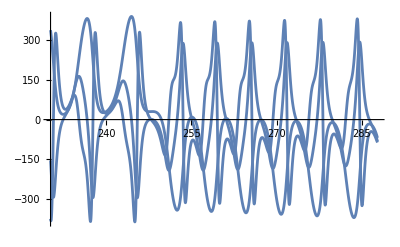

-Graphics3D-

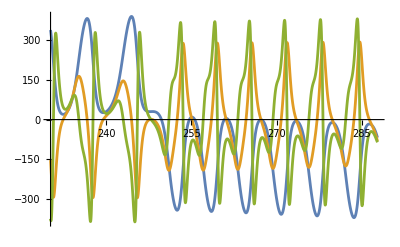

```mathematica
{y1sol,y2sol,y3sol}=NDSolveValue[{y1'[t]==y2[t],y2'[t]==y3[t],y3'[t]==-a*y3[t]+b*y2[t]-c*y2[t]^3-y1[t],y1[0]==0,y2[0]==1,y3[0]==0},{y1,y2,y3},{t,0,TMax}];

ParametricPlot3D[{y1sol[t],y2sol[t],y3sol[t]},{t,.8*TMax,TMax},PlotLabel->"Phase Plot - Once Around",PlotLegends->{"y","y'","y''"},AxesLabel->{"y","y'","y''"},PlotRange->All,PlotPoints->100]
Plot[{y1sol[t],y2sol[t],y3sol[t]},{t,0.8 TMax,TMax}]
```